## Making a difference between first and last child (3)

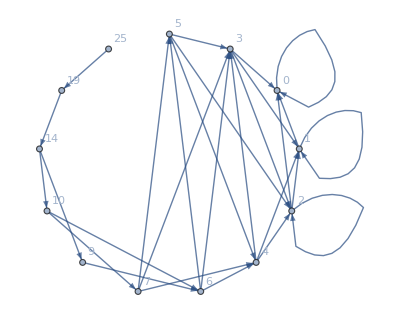

```mathematica
g53f=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==3&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==3&]],{child,Flatten[Map[First,all[k,"children"]]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

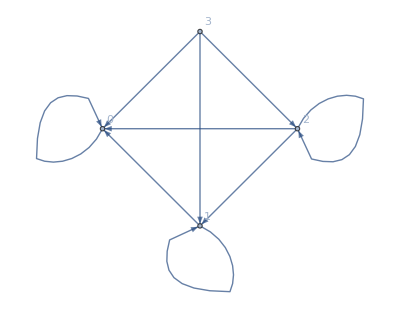

```mathematica
With[{g=NeighborhoodGraph[g53f,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

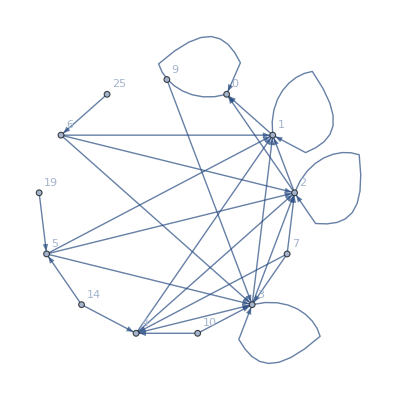

```mathematica
g53l=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==3&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==3&]],{child,Flatten[Map[Last,all[k,"children"]]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

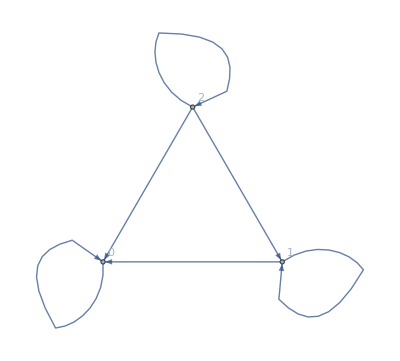

```mathematica
With[{g=NeighborhoodGraph[g53l,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

## Making a difference between first and last child (4)

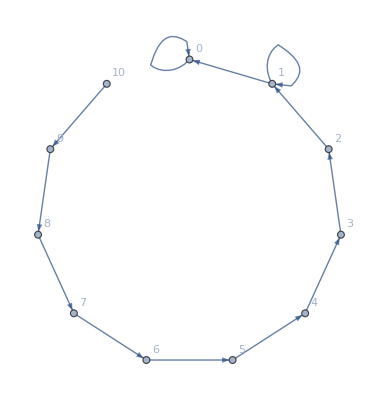

```mathematica
g54f=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[Map[First,all[k,"children"]]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

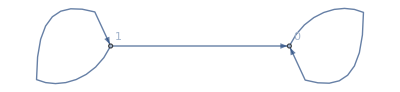

```mathematica
With[{g=NeighborhoodGraph[g54f,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

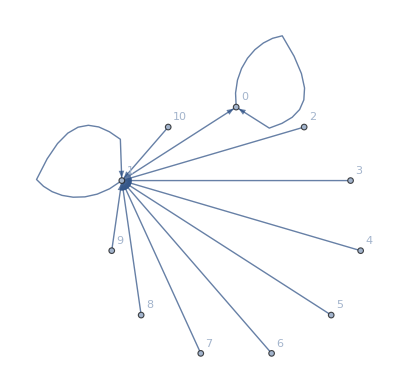

```mathematica
g54l=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[Map[Last,all[k,"children"]]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

```mathematica
With[{g=NeighborhoodGraph[g54l,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

-Graphics-

## Making a difference between first and last child (4) - six nodes

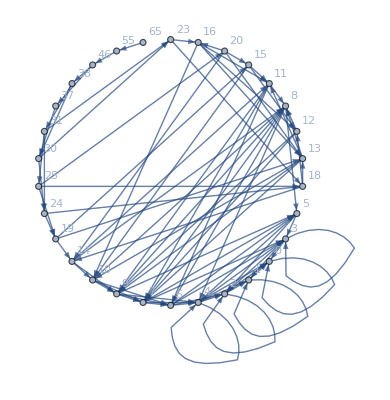

```mathematica
g64f=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[Map[First,all[k,"children"]]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

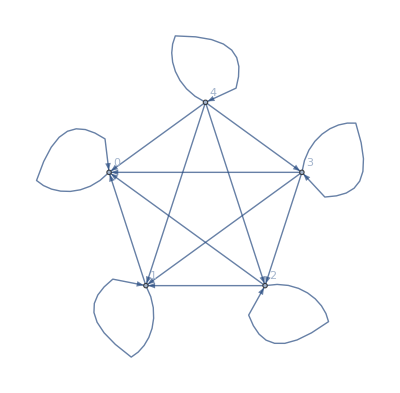

```mathematica
With[{g=NeighborhoodGraph[g64f,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

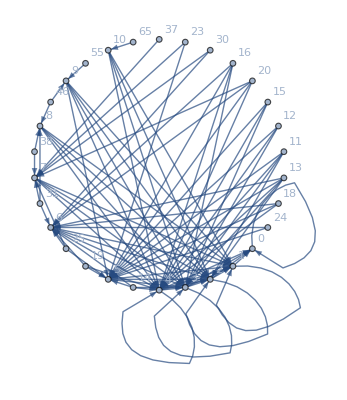

```mathematica
g64l=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[Map[Last,all[k,"children"]]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

```mathematica
With[{g=NeighborhoodGraph[g64l,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

-Graphics-

## Making a difference between first and last child (4) - six nodes

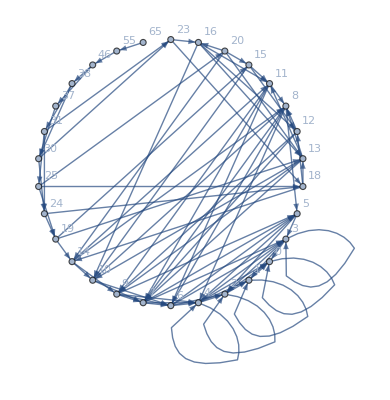

```mathematica
g64f=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[Map[First,all[k,"children"]]]}],
{k,Select[Keys[all],VertexCount[all[#,"graph"]]==6&]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

```mathematica
With[{g=NeighborhoodGraph[g64f,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

-Graphics-

```mathematica
g64l=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[Map[Last,all[k,"children"]]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

-Graphics-

```mathematica
With[{g=NeighborhoodGraph[g64l,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

-Graphics-